From here:
https://www.researchgate.net/figure/223020684_fig3_Figure-6-A-typical-single-photoelectron-waveform-This-graph-shows-the-measurement-by

```mathematica
pathOutput=NotebookDirectory[]<>"../";
```

```mathematica
InitialWaveform={0.2737,2.274,6.358,8.274,7.453,5.326,2.884,1.516,1.116,0.6316,0.04211,0.1684,0.4842,0.04211,-0.2105,0.1684,0.2737};
Length@InitialWaveform
```

17

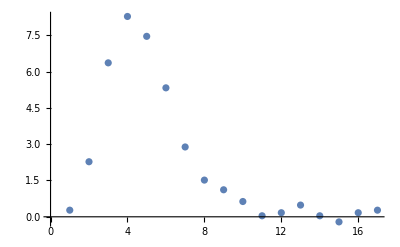

```mathematica
ListPlot[InitialWaveform]
```

```mathematica
FUNC=Interpolation[InitialWaveform];
```

```mathematica
Resolution=1/(2^12-1.)*2500
```

0.610501

```mathematica
Waveform12Bit=Round[Table[FUNC[i],{i,1,17,0.1}],Resolution];
Waveform12Bit=Round[Waveform12Bit,0.0001]
```

{0.,0.,0.,0.6105,0.6105,0.6105,1.221,1.221,1.8315,1.8315,2.442,2.442,3.0525,3.663,3.663,4.2735,4.884,4.884,5.4945,6.105,6.105,6.7155,6.7155,7.326,7.326,7.326,7.9365,7.9365,7.9365,7.9365,8.547,8.547,8.547,8.547,7.9365,7.9365,7.9365,7.9365,7.9365,7.326,7.326,7.326,7.326,6.7155,6.7155,6.7155,6.105,6.105,6.105,5.4945,5.4945,4.884,4.884,4.2735,4.2735,4.2735,3.663,3.663,3.0525,3.0525,3.0525,2.442,2.442,2.442,2.442,1.8315,1.8315,1.8315,1.8315,1.8315,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,1.221,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.6105,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.6105,0.6105,0.6105,0.6105,0.,0.}

```mathematica
randomBackground=Table[0.3*(Random[])/(1)-0.02,{i,1,200}];
```

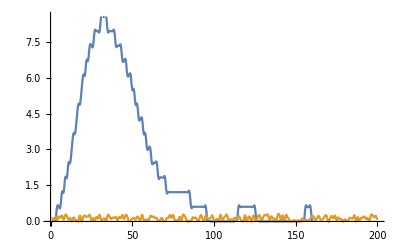

```mathematica
ListPlot[{Waveform12Bit,randomBackground},PlotRange->All,Joined->True,InterpolationOrder->2]
```

```mathematica
Export[pathOutput<>"Waveform12Bit.dat",Waveform12Bit]
```

/Users/chaffy/Work/Repository_MilliCharged/milliQan/SourceFiles/GenerateDistributions/../Waveform12Bit.dat

```mathematica
Export[pathOutput<>"Waveform.dat",InitialWaveform]
```

/Users/chaffy/Work/Repository_MilliCharged/milliQan/SourceFiles/GenerateDistributions/../Waveform.dat